```mathematica
Simple Clock Models
                           				Jaekyoung Kim Daniel B. Forger
```

```mathematica
Single Negative Feedback Loop
```

```mathematica
Initial Conditions
```

```mathematica
(*Initial Condition for the multi-state variable x[j][k][l][m][n]*)
atwo={m[0]==1,pc[0]==1,p[0]==1};
```

```mathematica
Parameters
```

```mathematica
(*Disociation Constant*)
Kd=10^(-5);
(*Activator Concenration*)
A=0.0659;
(*Producation rate of M, Pc and P*)
ao=1;at=1;ah=1;
(*Degradation rate of M, Pc and P*)
b=1;
```

```mathematica
Equations
```

```mathematica
aone={m'[t]==ao*(1-p[t]/A-Kd/A+Sqrt[(1-p[t]/A-Kd/A)^2+4*Kd/A])/2-b*m[t],pc'[t]==at*m[t]-b*pc[t],p'[t]==ah*pc[t]-b*p[t]};
```

```mathematica
Differential Equations Solver
```

```mathematica
qrto=NDSolve[Join[aone,atwo],{m,pc,p},{t,0,100},MaxSteps->10000000,MaxStepSize->0.01];
```

```mathematica
Plot
```

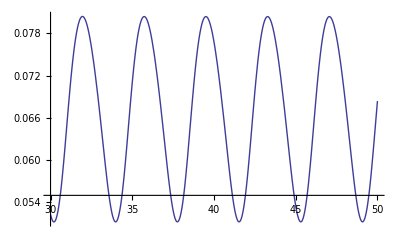

```mathematica
(*P*)
Plot[p[t]/.qrto,{t,30,50}]
```

```mathematica
Negative-Negative Feedback Loop
```

```mathematica
Initial Conditions
```

```mathematica
(*Initial Condition for the multi-state variable x[j][k][l][m][n]*)
atwo={m[0]==1,pc[0]==1,p[0]==1,A[0]==1,r[0]==1};
```

```mathematica
Parameters
```

```mathematica
(*Disociation Constant*)
Kd=10^(-5);
(*Producation rate of M, Pc, P, and R*)
ao=1;at=1;ah=1;ro=1;
(*Producation rate of A*)
rt=0.0043;
(*Degradation rate of M, Pc and P*)
b=1;
(*Degradation rate of R and A*)
d=0.2;
```

```mathematica
Equations
```

```mathematica
aone={m'[t]==ao*(1-p[t]/A[t]-Kd/A[t]+Sqrt[(1-p[t]/A[t]-Kd/A[t])^2+4*Kd/A[t]])/2-b*m[t],pc'[t]==at*m[t]-b*pc[t],p'[t]==ah*pc[t]-b*p[t],r'[t]==ro*(1-p[t]/A[t]-Kd/A[t]+Sqrt[(1-p[t]/A[t]-Kd/A[t])^2+4*Kd/A[t]])/2-d*r[t],A'[t]==rt/(r[t])-d*A[t]};
```

```mathematica
Differential Equations Solver
```

```mathematica
qrtt=NDSolve[Join[aone,atwo],{m,pc,p,A,r},{t,0,100},MaxSteps->1000000,MaxStepSize->0.1];
```

```mathematica
Plot
```

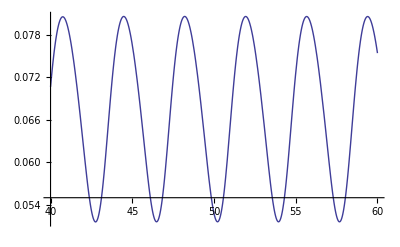

```mathematica
(*P*)
Plot[p[t]/.qrtt,{t,40,60}]
```

```mathematica
Positive-Negative Feedback Loop
```

```mathematica
Initial Conditions
```

```mathematica
(*Initial Condition for the multi-state variable x[j][k][l][m][n]*)
atwo={m[0]==1,pc[0]==1,p[0]==1,A[0]==1,r[0]==1};
```

```mathematica
Parameters
```

```mathematica
(*Disociation Constant*)
Kd=10^(-5);
(*Producation rate of M, Pc, P, and R*)
ao=1;at=1;ah=1;ro=1;
(*Producation rate of A*)
rt=0.0395;
(*Degradation rate of M, Pc and P*)
b=1;
(*Degradation rate of R and A*)
d=0.2;
```

```mathematica
Equations
```

```mathematica
aone={m'[t]==ao*(1-p[t]/A[t]-Kd/A[t]+Sqrt[(1-p[t]/A[t]-Kd/A[t])^2+4*Kd/A[t]])/2-b*m[t],pc'[t]==at*m[t]-b*pc[t],p'[t]==ah*pc[t]-b*p[t],r'[t]==ro*(1-p[t]/A[t]-Kd/A[t]+Sqrt[(1-p[t]/A[t]-Kd/A[t])^2+4*Kd/A[t]])/2-d*r[t],A'[t]==rt*r[t]-d*A[t]};
```

```mathematica
Differential Equations Solver
```

```mathematica
qrth=NDSolve[Join[aone,atwo],{m,pc,p,A,r},{t,0,200},MaxSteps->1000000,MaxStepSize->0.1];
```

```mathematica
Plot
```

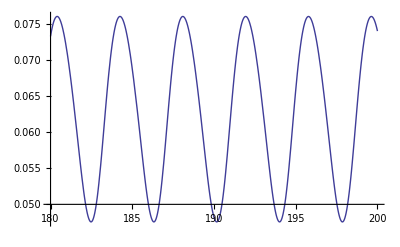

```mathematica
(*P*)
Plot[p[t]/.qrth,{t,180,200}]
```